# Phase Transition

## Effective Potential

### Interpolate thermal intergral

```mathematica
JB[x_]:=NIntegrate[z^2*Log[1-Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*bosonic field contributions*)
JF[x_]:=NIntegrate[z^2*Log[1+Exp[-Sqrt[z^2+x]]],{z,0,Infinity}]
(*fermionic field contributions*)
(*Cross check*)
fit11=Table[{ϕ,JB[ϕ]},{ϕ,10^(-1),200,.1}];
JBfit11[ϕ_]=Fit[fit11,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit12=Table[{ϕ,JB[ϕ]},{ϕ,10^(-3),10^(-1),10^(-3)}];
JBfit12[ϕ_]=Fit[fit12,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit13=Table[{ϕ,JB[ϕ]},{ϕ,0,10^(-3),10^(-6)}];
JBfit13[ϕ_]=Fit[fit13,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit21=Table[{ϕ,JF[ϕ]},{ϕ,10^(-1),200,.1}];
JFfit21[ϕ_]=Fit[fit21,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit22=Table[{ϕ,JF[ϕ]},{ϕ,10^(-3),10^(-1),10^(-3)}];
JFfit22[ϕ_]=Fit[fit22,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
fit23=Table[{ϕ,JF[ϕ]},{ϕ,0,10^(-3),10^(-6)}];
JFfit23[ϕ_]=Fit[fit23,{1,ϕ^0.5,ϕ,ϕ^2,ϕ^3,ϕ^1.5,ϕ^4,ϕ^5,ϕ^2.5,ϕ^3.5,ϕ^4.5,ϕ^5.5,ϕ^6,ϕ^6.5,ϕ^7,ϕ^7.5,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
JBfit[x_]:=JBfit11[x]/;10^(-1)<x≤200
JBfit[x_]:=JBfit12[x]/;10^(-3)<=x≤10^(-1)
JBfit[x_]:=JBfit13[x]/;0<=x≤10^(-3)
JBfit[x_]:=0/;200<x
JFfit[x_]:=JFfit21[x]/;10^(-1)<x≤200
JFfit[x_]:=JFfit22[x]/;10^(-3)<=x≤10^(-1)
JFfit[x_]:=JFfit23[x]/;0<=x≤10^(-3)
JFfit[x_]:=0/;200<x;
```

### Effective Potential

```mathematica
vR=15000;
g=0.65;
gX=√(0.36^2 g^2/(g^2-0.36^2));
yt=0.7;
yN=0.65;
mt[ϕ_]:=yt^2 ϕ^2/2;
mN[ϕ_]:=yN^2 ϕ^2/2
mW[ϕ_]:=g^2 ϕ^2/4;
mZ[ϕ_]:=(g^2+gX^2)ϕ^2/4;
mH[λ_,ϕ_]:=3λ ϕ^2-λ vR^2;(*Physical Subscript[h, R]*)
mX[λ_,ϕ_]:=λ ϕ^2-λ vR^2;(*Goldstone bosons*)
mgauge=({{g^2 x1^2/4+11/6 g^2 x2^2, -g gX x1^2/4}, {-g gX x1^2/4, gX^2 x1^2/4+29/18 g^2 x2^2}});
(*x1 is the field. x2 is the temperature. This is the mixing between W3 and Subscript[B, X]*)
gaugeL=Eigenvalues[mgauge]//FullSimplify;
B[λ_]:=1/(64 π^2 vR^4)(6 mW[vR]^2+3 mZ[vR]^2+mH[λ,vR]^2-12 mt[vR]^2-8 mN[vR]^2);
mWL[ϕ_,T_]:=1/4 g^2 ϕ^2+11/6 g^2 T^2;(*longitudal mode for W+ and W-, or W1 and W2*)
mBL[ϕ_,T_]:=gaugeL[[1]]/.{x1->ϕ,x2->T};(*SM B particle, massless*)
mZL[ϕ_,T_]:=gaugeL[[2]]/.{x1->ϕ,x2->T};(*Zprime particle*)
mHT[λ_,ϕ_,T_]:=3λ ϕ^2-λ vR^2+1/2 λ T^2+1/4*yt^2 T^2+1/8 g^2 T^2+1/16(g^2+gX^2)T^2;
mXT[λ_,ϕ_,T_]:=λ ϕ^2-λ vR^2+1/2 λ T^2+1/4*yt^2 T^2+1/8 g^2 T^2+1/16(g^2+gX^2)T^2;
V0[λ_,ϕ_]:=-1/2 λ vR^2 ϕ^2+λ/4 ϕ^4;
VB[λ_,ϕ_]:=2B[λ] vR^2 ϕ^2-3/2 B[λ] ϕ^4+B[λ] ϕ^4 Log[ϕ^2/vR^2];
VFT[λ_,ϕ_,T_]:=T^4/(2 π^2)(6JBfit[mW[ϕ]/T^2]+3JBfit[mZ[ϕ]/T^2]+JBfit[Abs[mH[λ,ϕ]]/T^2]+3JBfit[Abs[mX[λ,ϕ]]/T^2]-12JFfit[mt[ϕ]/T^2]-8JFfit[mN[ϕ]/T^2]);
VFTre[λ_,ϕ_,T_]:=T^4/(2 π^2)(4JBfit[mW[ϕ]/T^2]+2JBfit[mWL[ϕ,T]/T^2]+2JBfit[mZ[ϕ]/T^2]+JBfit[mZL[ϕ,T]/T^2]+JBfit[mBL[ϕ,T]/T^2]+JBfit[Abs[mHT[λ,ϕ,T]]/T^2]+3JBfit[Abs[mXT[λ,ϕ,T]]/T^2]-12JFfit[mt[ϕ]/T^2]-8JFfit[mN[ϕ]/T^2]);
Vring[λ_,ϕ_,T_]:=T/(12π)(2(mW[ϕ]^(3/2)-mWL[ϕ,T]^(3/2))+(mZ[ϕ]^(3/2)-mZL[ϕ,T]^(3/2))-mBL[ϕ,T]^(3/2)+(Abs[mH[λ,ϕ]]^(3/2)-Abs[mHT[λ,ϕ,T]]^(3/2))+3(Abs[mX[λ,ϕ]]^(3/2)-Abs[mXT[λ,ϕ,T]]^(3/2)));
Vefftot[λ_,ϕ_,T_]:=V0[λ,ϕ]+VB[λ,ϕ]+VFT[λ,ϕ,T]-(V0[λ,10^-3]+VB[λ,10^-3]+VFT[λ,10^-3,T]);
VeffArnold[λ_,ϕ_,T_]:=V0[λ,ϕ]+VB[λ,ϕ]+VFT[λ,ϕ,T]+Vring[λ,ϕ,T]-(V0[λ,10^-3]+VB[λ,10^-3]+VFT[λ,10^-3,T]+Vring[λ,10^-3,T]);
```

```mathematica
Vefftot[0.011,4000,4000]
```

6.70686×10^11

```mathematica
Plot[Vefftot[0.015,ϕ,4200],{ϕ,0,6000}]
```

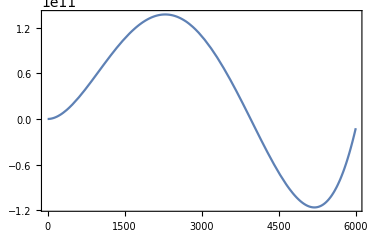

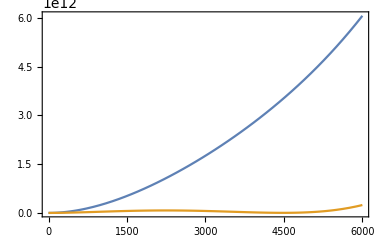

```mathematica
Plot[{Vefftot[0.011,ϕ,3957.],VeffArnold[0.011,ϕ,3957.]},{ϕ,0,6000}]
```

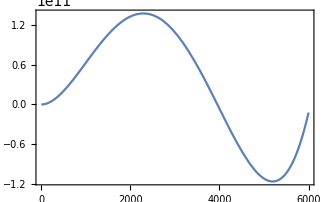

```mathematica
Plot[Vefftot[0.015,ϕ,4200],{ϕ,0,6000}]
```

```mathematica
xwidth=10^3;
xwidtha=10;
ϕmin=3000;
ϕmax=6000;
Tmax=5000;
x0[λ_,T_]:=Catch[Do[If[VeffArnold[λ,x,T]<0,Throw[x]],{x,ϕmin,ϕmax,xwidth}]]
x1[λ_,T_,xp_]:=Catch[Do[If[VeffArnold[λ,x,T]<0,Throw[x]],{x,xp-1.1*10^3,xp+10^3,xwidtha}]]
```

```mathematica
λ=0.013;
t0=Catch[Do[If[x0[λ,T]>0,Throw[T]],{T,Tmax,1,-10^3}]];
t1=Catch[Do[If[x0[λ,T]>0,Throw[T]],{T,t0+10^3,t0,-10^2}]];
t2=Catch[Do[If[x0[λ,T]>0,Throw[T]],{T,t1+10^2,t1,-10}]];
t3=Catch[Do[If[x0[λ,T]>0,Throw[T]],{T,t2+10,t2,-1}]];
Tc=Catch[Do[If[x0[λ,T]>0,Throw[T]],{T,t3+1,t3,-0.1}]];
xp=x0[λ,Tc];
t00=Catch[Do[If[x1[λ,T,xp]>0,Throw[T]],{T,Tmax,1,-10^3}]];t01=Catch[Do[If[x1[λ,T,xp]>0,Throw[T]],{T,t00+10^3,t00,-10^2}]];
t02=Catch[Do[If[x1[λ,T,xp]>0,Throw[T]],{T,t01+10^2,t01,-10}]];t03=Catch[Do[If[x1[λ,T,xp]>0,Throw[T]],{T,t02+10,t02,-1}]];
Tc1=Catch[Do[If[x1[λ,T,xp]>0,Throw[T]],{T,t03+1,t03,-0.1}]]
xp1=x1[λ,Tc1,xp]
xp1/Tc1
```

4188.1

4220.

1.00762

```mathematica
x0[0.015,5000]
```

```mathematica
SetDirectory[NotebookDirectory[]]
<<anybubble.m
<<powell.m
Options[FindBubble]
```

/Users/isaac/Dropbox/Project/2021-9-local_EWBG_parity/code

{Verbose→False,SpaceTimeDimension→3,StartAnalyticFraction→1/100,EndAnalyticFraction→1/100,MaxIntervalGrowth→30,MaxReadjustments→20,InitialProfilePoints→{},PowellVerbosity→1,MaxIterations→500,AccuracyGoal→Automatic,WorkingPrecision→MachinePrecision}

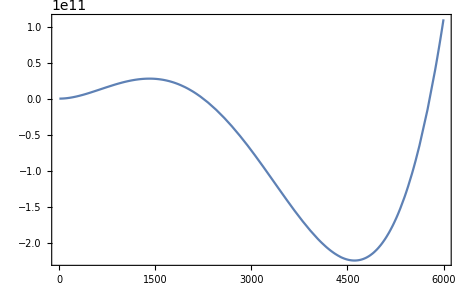

```mathematica
Plot[VeffArnold[0.016,ϕ,4505.],{ϕ,0,6000}]
```

```mathematica
T1=4505.0;
fitting=Table[{ϕ,VeffArnold[0.016,ϕ,T1]},{ϕ,1,6000,10}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
xr=x/.Minimize[{Vfit[x]-Vfit[0],{3000<x<6000}},x][[2]];
SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/T1)[[1]]
```

.......................

138.085

........................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................

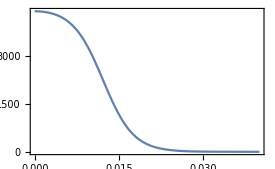

```mathematica
Plot[FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}][[2]][r],{r,0,0.04}]
```

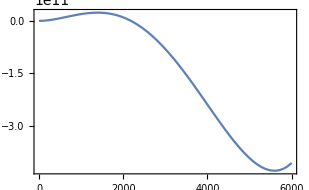

```mathematica
Plot[VeffArnold[0.009,ϕ,3695.],{ϕ,0,6000}]
```

```mathematica
T1=3687.2;
fitting=Table[{ϕ,VeffArnold[0.009,ϕ,T1]},{ϕ,1,6000,10}];
Vfit[ϕ_]=Fit[fitting,{1,ϕ,ϕ^2,ϕ^3,ϕ^4,ϕ^5,ϕ^6,ϕ^7,ϕ^8,ϕ^9,ϕ^10,ϕ^11,ϕ^12,ϕ^13,ϕ^14,ϕ^15,ϕ^16,ϕ^17,ϕ^18,ϕ^19,ϕ^20},ϕ];
xr=x/.Minimize[{Vfit[x]-Vfit[0],{3000<x<6000}},x][[2]];
SbyT=(FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}]/T1)[[1]]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

...............................

139.133

................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................................

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

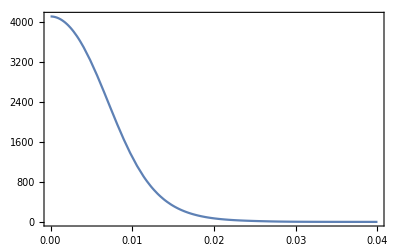

```mathematica
Plot[FindBubble[Vfit[x[1]]-Vfit[0],x,{xr},{0}][[2]][r],{r,0,0.04}]
```